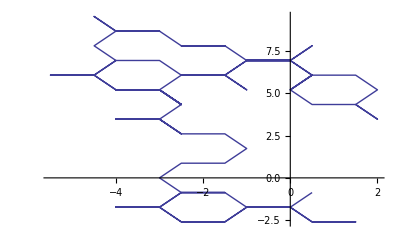

```mathematica
ListLinePlot[Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[3]/3+π Mod[i,2]]],{i,100}]]]
```

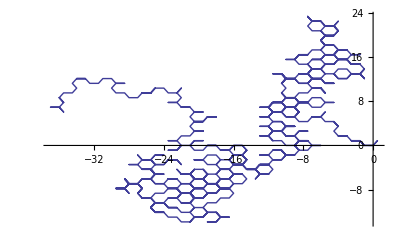

```mathematica
ListLinePlot[Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[3]/3+π Mod[i,2]]],{i,1000}]]]
```

```mathematica
(* questo è quello corretto con RandomInteger[2] *)
```

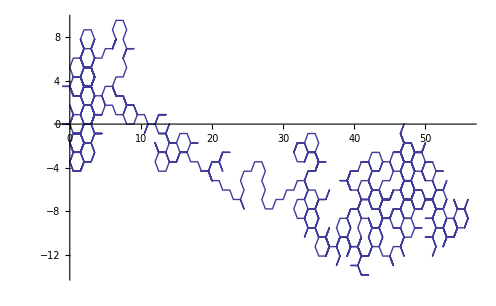

```mathematica
ListLinePlot[Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[2]/3+π Mod[i,2]]],{i,1000}]]]
```

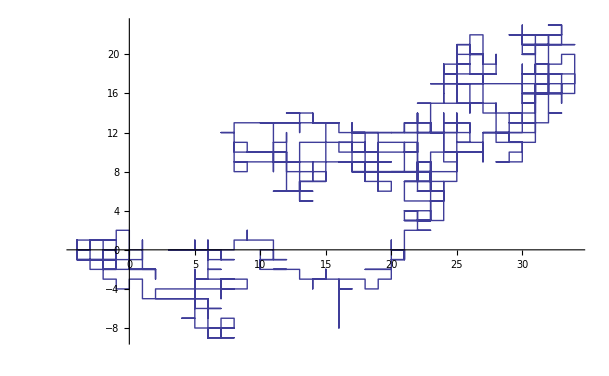

```mathematica
ListLinePlot[Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[3]/4+π  Mod[i,2]]],{i,1000}]]]
```

```mathematica
Mod[1,2]
```

1

```mathematica
Mod[2,3]
```

2

```mathematica
Mod[11,2]
```

1

```mathematica
2 π RandomInteger[3]/4+π  Mod[1,2]
```

(3 π)/2

```mathematica
Through[{Cos,Sin}[2 π RandomInteger[2]/4+π  Mod[1,2]]]
```

{-1,0}

```mathematica
?Through
```

Through[p[f_1,f_2][x]] gives p[f_1[x],f_2[x]]. 
Through[expr,h] performs the transformation wherever h occurs in the head of expr.

```mathematica
?Mod
```

Mod[m,n] gives the remainder on division of m by n. 
Mod[m,n,d] uses an offset d.

```mathematica
Mod[6,2]
```

0

```mathematica
Mod[7,2]
```

1

```mathematica
(* Questo è corretto su reticolo quadrato *)
```

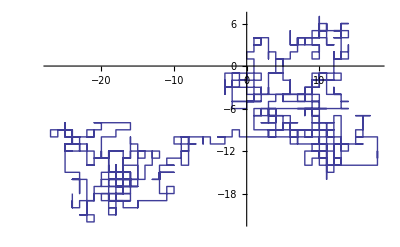

```mathematica
ListLinePlot[Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[3]/4]],{1000}]]]
```

```mathematica
Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[3]/4]],{100}]]
```

{{0,-1},{0,0},{1,0},{0,0},{0,-1},{0,-2},{-1,-2},{-1,-1},{-2,-1},{-2,-2},{-2,-3},{-3,-3},{-3,-2},{-2,-2},{-2,-3},{-2,-2},{-2,-3},{-1,-3},{-2,-3},{-2,-4},{-2,-3},{-1,-3},{0,-3},{0,-2},{0,-1},{0,-2},{0,-1},{0,-2},{1,-2},{1,-3},{1,-2},{1,-3},{0,-3},{-1,-3},{-1,-4},{-2,-4},{-2,-5},{-3,-5},{-3,-4},{-3,-5},{-4,-5},{-3,-5},{-2,-5},{-3,-5},{-3,-4},{-3,-3},{-2,-3},{-2,-2},{-1,-2},{-1,-1},{-1,0},{-2,0},{-2,-1},{-1,-1},{-2,-1},{-3,-1},{-3,-2},{-2,-2},{-2,-1},{-2,0},{-2,1},{-1,1},{-1,2},{-2,2},{-3,2},{-4,2},{-4,3},{-4,2},{-4,1},{-5,1},{-4,1},{-4,2},{-4,3},{-4,4},{-5,4},{-5,5},{-6,5},{-6,6},{-6,7},{-5,7},{-5,8},{-4,8},{-3,8},{-2,8},{-2,7},{-2,6},{-1,6},{0,6},{-1,6},{-1,7},{-1,6},{-2,6},{-3,6},{-3,5},{-2,5},{-2,4},{-3,4},{-3,5},{-3,4},{-4,4}}

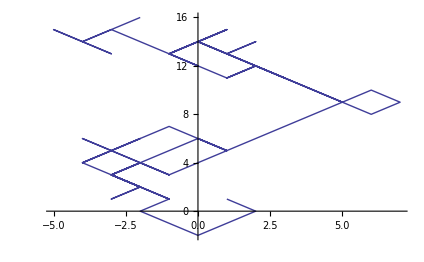

```mathematica
ListLinePlot[Accumulate@RandomChoice[{-1,1},{100,2}]]
```

```mathematica
Accumulate@RandomChoice[{-1,1},{100,2}]
```

{{-1,1},{0,2},{1,1},{0,2},{-1,3},{-2,4},{-1,5},{0,6},{-1,7},{0,6},{1,5},{0,4},{1,3},{2,2},{1,3},{2,4},{3,5},{2,4},{3,5},{4,6},{3,7},{2,8},{1,7},{2,6},{1,5},{0,6},{-1,7},{0,6},{1,7},{0,8},{-1,9},{-2,10},{-1,9},{0,8},{1,9},{2,8},{3,9},{4,8},{3,9},{2,8},{3,9},{2,8},{1,9},{2,10},{1,11},{2,10},{3,11},{2,12},{3,11},{4,12},{5,13},{6,12},{7,11},{8,12},{9,11},{8,12},{9,13},{8,12},{9,11},{10,10},{11,11},{10,10},{9,11},{8,10},{7,11},{6,10},{5,11},{4,10},{5,9},{4,10},{5,9},{6,8},{5,9},{6,10},{5,11},{4,10},{5,11},{4,12},{5,11},{4,12},{3,11},{2,12},{1,13},{0,12},{-1,11},{0,10},{1,11},{0,12},{-1,11},{-2,12},{-1,11},{0,12},{-1,13},{0,14},{1,13},{0,12},{-1,13},{0,14},{1,13},{0,12}}

```mathematica
RandomChoice[{-1,1},{100,2}]
```

{{1,-1},{-1,-1},{1,1},{1,-1},{1,1},{1,1},{1,-1},{-1,1},{1,-1},{1,1},{-1,1},{-1,1},{-1,1},{-1,-1},{1,-1},{-1,-1},{1,1},{1,-1},{-1,-1},{1,-1},{1,1},{-1,-1},{-1,1},{1,1},{-1,-1},{-1,-1},{-1,1},{-1,1},{1,1},{-1,-1},{-1,1},{-1,-1},{-1,-1},{1,-1},{1,1},{-1,-1},{1,-1},{-1,-1},{-1,-1},{1,1},{-1,1},{1,-1},{1,1},{-1,1},{1,-1},{1,1},{1,-1},{-1,-1},{1,1},{-1,1},{-1,-1},{1,-1},{-1,1},{-1,-1},{-1,-1},{-1,1},{1,1},{-1,-1},{1,1},{1,-1},{-1,1},{1,1},{-1,1},{1,-1},{-1,-1},{1,-1},{-1,1},{1,-1},{1,1},{1,1},{1,1},{-1,1},{-1,1},{-1,-1},{1,-1},{-1,1},{1,1},{1,-1},{1,-1},{1,1},{-1,-1},{-1,1},{1,1},{-1,1},{-1,1},{1,-1},{1,-1},{1,-1},{1,1},{1,1},{-1,1},{-1,1},{-1,1},{1,1},{-1,-1},{1,-1},{-1,-1},{1,-1},{-1,-1},{-1,1}}

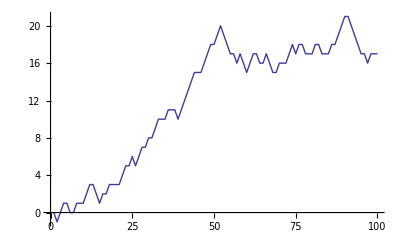

```mathematica
ListLinePlot[Accumulate@RandomInteger[{-1,1},100]]
```

```mathematica
RandomInteger[{-1,1},100]
```

{-1,1,-1,1,1,0,1,0,1,-1,0,0,1,1,-1,-1,0,0,-1,-1,1,1,0,0,-1,-1,0,1,-1,0,-1,1,1,1,0,-1,1,1,-1,-1,1,1,0,0,0,0,0,1,0,1,1,1,-1,0,0,1,1,-1,0,-1,0,1,-1,1,0,0,-1,0,1,0,0,1,1,-1,0,0,0,1,1,-1,-1,-1,0,0,-1,0,1,0,0,0,-1,0,0,0,-1,0,0,1,0,0}

```mathematica
Accumulate[%]
```

{-1,0,-1,0,1,1,2,2,3,2,2,2,3,4,3,2,2,2,1,0,1,2,2,2,1,0,0,1,0,0,-1,0,1,2,2,1,2,3,2,1,2,3,3,3,3,3,3,4,4,5,6,7,6,6,6,7,8,7,7,6,6,7,6,7,7,7,6,6,7,7,7,8,9,8,8,8,8,9,10,9,8,7,7,7,6,6,7,7,7,7,6,6,6,6,5,5,5,6,6,6}

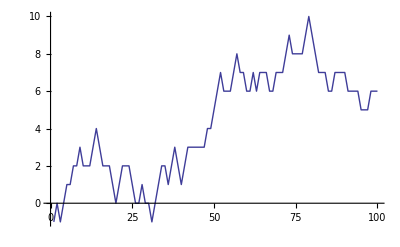

```mathematica
ListLinePlot[%]
```

```mathematica
{Cos,Sin}[2 π RandomInteger[3]/4]
```

{Cos,Sin}[π]